# Pricing a Call Option Premium Using Regression Analysis of the Black-Scholes Pricing Model

Spencer Lyon
Brigham Young University

Abstract: Financial derivatives and options have been subject to extensive efforts to correctly identify, model, and price them. Starting in the 1970’s, this emerging field of study has been the focus of much of modern finance. Paramount in this exploration is the Black Scholes equation. In this paper I briefly explain and review the equation and proceed to develop a similar model that will allow Ordinary Least Squares methodologies to be applied to the pricing of option premiums. My analysis focuses on the ability of my equation to accurately price options that are strictly in or out of the money.

## I. Introduction

A call option is a financial contract between two parties that gives one party the right to buy a particular security on a specified date (expiration date) at a specified price (strike price) [1].The seller of the call will be obligated to sell his shares of a particular security to the call buyer if the buyer chooses to exercise the option. An option is only exercised if it is “in the money,” meaning the current price of the stock is above the strike price. Exercising the option will allow the call holder, to buy at the strike price then sell at the market price;  realizing an immediate profit of the difference in the two. On the other hand, if the current market price is below the strike price the option is said to be “out of the money” and will not be exercised.

The pricing of these options has been a topic of extensive academic research and professional inquiry for the past 40 or so years. This hype started for the most part in 1973 when Fischer Black and Myron Scholes developed a formula for pricing the premium on a call option. Black was an Applied Mathematics PhD, but was highly educated in Physics also. He knew of a classic partial differential equation in physics called the heat transfer equation and proposed that the same underlying mathematics might be applied to finance; specifically option pricing [2].With the help of Scholes, Black was able to create what is known today as the Black-Scholes equation:

(∂V)/(∂t)+1/2 σ^2 S^2(∂^2 V)/(∂S^2)+rS(∂V)/(∂S)-rV=0

Where V is the price of the underlying option, t is time, S is the price of the stock, r is the annualized risk-free interest rate, and σ is the volatility of the stock’s returns (measured by the square root of the quadratic variation of the stock’s log price process).

In this report we care about the value of a call option in particular and the solution of the Black-Scholes equation for a call option is as follows [3]:

C(S,t) = N(d_1)S - N(d_2)K e^(-r(T-t)),
d_1 = (ln(S/K) + (r+σ^2/2)(T-t))/(σ √(T-t)),
d_2 =  (ln(S/K) + (r-σ^2/2)(T-t))/(σ √(T-t))= d_1-σ √(T-t)
N(x) = 1/(√(2π))∫_(-∞)^z e^(-z^2/2)dz

Where the variables are the same as above and K is the strike price, C(s,t) is the call option premium as a function of the stock price and time, and N is the standard normal cumulative distribution.

The purpose of my report is to create a form of the Black Scholes equation that will allow me to use ordinary least squares (OLS) techniques to examine the effectiveness of the BS equation in pricing call option premiums for options that are “in the money” and those that are “out of the money”.

## II. Description of the Model and Data

### The Model

In order to apply OLS regression analysis on the Black Scholes equation, the equation needed to be transformed in such a way that OLS would be applicable. As seen in equation (2) above, the price of a call-option premium is a function of the underlying stock price (p), the time until expiration (T-t), the volatility of the stock (σ), and the current risk-free interest rate (r). Having this in mind I decided to do a generic second order Taylor series approximation of the option price as a function of these variables [4]. The functional form associated with my model is as follows:

K(p,r,t,σ) = β_1+β_2 p+β_3 σ + β_4 t + β_5 r+β_6 p^2+β_7 σ^2+β_8 t^2+β_9 r^2+β_10 p*σ+β_11 p*t+β_12 p*r+β_13 σ*t+β_14 σ*r+β_15 t*r

The inclusion of the above variables is justified by financial theory and the Black Scholes equation. Basic theory says that an option for a stock should be dependent on the underlying stock price (p). If this price changes, options at particular strike prices become more or less valuable and thus their price changes. The time until expiration(t) is the next obvious indicator for price of options. As time runs out on the life of the option, it will become even more valuable if it is in the money because the probability of the stock moving out of the money is lower. The opposite is also true, if the option is out of the money, as time remaining decreases so does the value (price) of the option because the chance of the stock price moving into the money is very low. The volatility of the stock (σ) is also very important in the price of an option. When an individual enters an options contract they are taking a more severe long or short position on the movement of the stock. A shift in the price of a stock from 33 to 35 dollars represents about a 5% increase in the stock price. In this same scenario, a call option with a strike price of 34 dollars might move from $0.50 to $1.90, representing about a 125% increase in the option price. Thus, the inclusion of the stock’s volatility is a theoretically viable choice. Finally we have the non-risk interest rate (r). This has a more indirect effect. Economic theory suggests that the risk-free rate of return is the opportunity cost an investor faces when they buy/sell an option contract. A high interest rate will entice more risk-adverse investors to take this risk-free return instead of the more risky stock option investment.

An explanation for the chosen functional form stems from the theory discussed above, the Black Scholes equation itself, and the needs required by an OLS regression. The B-S equation, and others in financial asset pricing theory, suggest that the price of a financial option has a dependent relationship with the Variables listed above. In order to be able to do a least-squares analysis of the factors I need to write the equation in a form that would have independent variables listed with linear coefficients associated with each one, or combination of them. A second order Taylor series expansion provides these properties, but remains general enough to still see the effects each of these variables has on the option price.

For this model and functional form for it I would expect that the price of the stock (p) would have the biggest impact on the price of the call. After all, the call is a derivative of the stock and the ultimate value is determined by the price of the stock. I would expect this impact to be positive. After that I would expect the time expiration (t) to have the next largest effect, but the direction is less clear. I would hypothesize that for an in the money call the time left would have an inverse relationship, meaning that as expiration time gets closer the call is worth more. The opposite would be true for an out of the money call. After (or alongside in importance) I would say that the volatility of the stock (σ) should have a positive effect on the price of any call. I believe this is true because as the stock is more volatile, the likelihood for a Positive upswing is greater (obviously the reverse is also true, but for the most part investors who participate in options trading are less risk adverse and usually that means more optimistic). Finally we have the interest rate (r), which I would expect to have a negative relationship with the price of the call. The higher the interest rate, the greater the incentive to invest in that asset instead of the option. As this happens the demand for the option decreases and the price falls as a result.

### The Data

The model will be estimated using information for the Walt Disney Company. (The choice of Disney has no theoretical significance, other than the fact that I love Disney!). I gathered the adjusted closing stock price (p in USD) for Disney from the period between June, 20th 2011 and November 18th, 2011. To have an estimate for σ I needed to have some measure of the change in the stock price during that period. For each day in our period I chose to take the standard deviation of the previous 45 trading days and I call that σ. This seemed appropriate Because the standard deviation is a measure of the movement of the stock and so is volatility. For the risk-free interest rate (r in 10’s of percent) I chose the annualized short term US Treasury Bill interest rate. Because of current economic conditions, this rate is abnormally low, but it was taken in the same period as all the other data and should be sufficient. The last piece of data was the price of the call option for November 2011 options. The closing stock price on the last trading day for the options (November 18th, 2011) was $35.63 so I chose strike prices of K = 33,34,35,36,37 to have a few in the money options  (K=33,34,35, in USD) and a few out of the money ones (K = 36,37, also in USD). (See Appendix for explanation of where the data was taken from).

#### Summary of Data

Variable | Observatios | Mean | Standard Dev. | Min. | Max.
K=33 | 44 | 1.94636 | .8966322 | .49 | 4
K=34 | 44 | 1.361364 | .6873697 | .31 | 2.94
K=35 | 44 | .8638636 | .4667812 | .19 | 1.92
K=36 | 44 | .5197727 | .2977629 | .01 | 1.3
K=37 | 44 | .2929545 | .1847258 | .01 | .92
p | 44 | 33.44 | 2.156826 | 29 | 36.7
σ | 44 | 17.04911 | .4044849 | 1.200547 | 2.728588
t | 44 | 29.31818 | 17.95961 | 0 | 59
r | 44 | 1.038636 | .1242951 | .8 | 1.3
p^2 | 44 | 1122.78 | 142.1444 | 841 | 1346.89
σ^2 | 44 | 3.066611 | 1.455062 | 1.441314 | 7.445194
t^2 | 44 | 1174.773 | 1092.344 | 0 | 6381
r^2 | 44 | 1.093864 | .2561451 | .64 | 1.69
p*σ | 44 | 57.14241 | 14.34702 | .3663832 | 88.16069
p*t | 44 | 947.6073 | 542.3684 | 0 | 1906.29
p*r | 44 | 34.76152 | 5.038911 | 35.624 | 47.164
σ*t | 44 | 48.4522 | 37.39611 | 0 | 160.9867
σ*r | 44 | 1.763636 | .430924 | .9604379 | 2.77602
t*r | 44 | 30.38409 | 18.42357 | 0 | 63.8

## III. Estimation Procedures

### Estimation

To begin the estimation procedure I first did a normal regression using the model (3) using K=each of the strike prices and obtained the following results:

My first concern after seeing these initial results was the existence of multicollinearity. By definition, multicollinearity exists when there is statistically significant correllation among the independent variables. I feared that there would be issues with multicollinearity for the sigma variable (calculated using the standard deviation of the previous 45 days stock price) because of how it is defined. By definition, if the stock price moves a lot in a small amount of time, the volatility (represented by my variable sigma) will be higher. These concerns were substantiated upon preforming the initial OLS regression that produced a large F statistic, representing the overall explanatory power of the model, and very small t statistics, representing issues with individual parameters. To overcome this issue I restructured my model and looked for those variables whose t-statistics were not significant at the α = 0.1 level for all 5 regressions and removed them from the model. These are highlighted in red above and were r^2 and s*r. The resulting model is as follows:

K(p,r,t,σ) = β_1+β_2 p+β_3 σ + β_4 t + β_5 r+β_6 p^2+β_7 σ^2+β_8 t^2+β_9 p*σ+β_10 p*t+β_11 σ*t+β_12 σ*r+β_13 t*r

After making these omissions I redid the regression for each of them and preformed a log-likelihood test to make sure that I wasn’t losing a significant portion of my explanatory power moving from the model in (3) to the model in (4). I took the before results with the 5 regression and they log-likelihoodvalue averaged to 55.2035 and after the average was 53.308 (see the appendix for the actual STATA printouts). This is a very small decrease in the average log-likelihood value so the changes made don’t destroy the explanatory ability of the model.

Econometric theory for Ordinary Least Squares (OLS) regressions rests on 5 distinct assumptions about the model and data.  In the next section we will define, explain, test for, and make any corrections necessary so that our model is in line with 3 of these 5 assumptions.

#### The Normality Assumption

This assumption states that the error terms must be normally distributed. If this assumption is not true the associated t and F statistics normally used in statistical inference will be invalid. Testing the normality assumption requires a test of the skewness and kurtosis of the regression. If the assumption were true in our model we would expect the skewness to be close to 0 and the kurtosis close to 3. To test these properties I performed a Jarque-Bera test and selected results are shown below (in each case we have eXX where XX represents the strike price being tested):

Variable | Pr(Skewness) | Pr(Kurtosis) | ajd χ^2 | Prob>χ^2
e33 | 0.5405 | .03119 | 1.47 | 0.4791
e34 | 0.1695 | 0.1695 | 3.98 | 0.1367
e35 | 0.6022 | 0.1353 | 2.66 | 0.2641
e36 | 0.0247 | 0.0849 | 7.16 | 0.0279
e37 | 0.2268 | 0.2171 | 3.18 | 0.2036

For these tests the null hypothesis is always that the distribution of the error terms is normal (H_0: normality). In each case except a strike price of $36 the null hypothesis is not rejected and we do not have to worry about severe non-normality. To correct for the normality issue in the K=36 regression I did a least absolute deviations (LAD) regression instead of the least squares regression and this gave us the maximum likelihood estimates for all the parameters in the regression. Comparative results for OLS and LAD regressions are shown in the table below (the top number is the coefficient value and the number below in parenthesis is the standard error for that estimate).

Variable | k =33 |  | k=34 |  | k=35 |  | k=36 |  | k=37 | 
 | OLS | LAD | OLS | LAD | OLS | LAD | OLS | LAD | OLS | LAD
p | -3.2500069
(1.194859) | -3.250069 
(1.229856) | -2.193462 
(1.107174) | -2.193462 
(1.326796) | -2.162417
(.7254697) | -2.162417
(.7769674) | -2.524739 
(.6062818) | -2.524739 
(.6955436) | -3.038973 
(.3588386) | -3.038973 
(.4597435)
σ | -7.742576
(2.681976) | -7.742576 
(2.272218) | -7.419269 
(2.485159) | -7.419269 
(2.564295) | -5.167932 
(1.628387) | -5.167932 
(1.822142) | -1.617983 
(1.360858) | -1.617983 
(1.360858) | .486258
(.805448) | .486258
(.7261706)
t | -.1820679
(.1747779) | -.1820679 
(.174606) | -.0271031 
(.1619518) | -.0271031 
(.2043547) | -.0166405 
(.106118) | -.0166405
( .1430602) | -.0249478
(.0886838) | -.0249478 
(.0886838) | -.2284746
( .0524891) | -.2284746
( .0582096)
r | -2.774696
(1.405764) | -2.774696 
(1.199488) | -3.503552 
(1.302602) | -3.503552 
(.8751817) | -1.934568 
(.8535231) | -1.934568 
(.5358036) | -.9299283 
(.132972) | -.9299283
(.7132972) | -.5358771 
(.4221776) | -.5358771 
(.3052101)
p^2 | .0510007
(.0164458) | .0510007
(.017081) | .0363157
(.0152389) | .036315
(.0183537) | .0340035
(.0099852) | .0340035
(.0104371) | .0387714
(.0083448) | .0387714
(.0083448) | .044309
(.004939) | .044309
(.0064616)
σ^2 | -.5966897
(.3164073) | -.5966897 
(.2767096) | -.4439363 
(.2931877) | -.4439363
( .2820814) | -.4260877 
(.1921097) | -.4260877 
(.2128816) | -.1553143 
(.1605478) | -.1553143 
(.1605478) | -.2098047 
(.0950231) | -.2098047 
(.0882846)
t^2 | .0005167
(.0005285) | .0005167
(.0005562) | .0000549
(.0004897) | .0000549
(.0005208) | -.0002977 
(.0003209) | -.0002977 
(.0003965) | -.0006506 
(.0002681) | -.0006506 
(.0002681) | -2.22e-06
(.0001587) | -2.22e-06
(.0001503)
p*σ | .2050254
(.0672341) | .2050254
(.0592232) | .1664814
(.0623001) | .1664814
(.062007) | .147783
(.0408218) | .147783
(.0443671) | .0593628
(.0341152) | .0593628
(.0341152) | .0025234
(.0201917) | .0025234
(.0187532)
p*t | .0020305
(.0042259) | .0020305
(.00435) | -.0017177 
(.0039158) | -.0017177 
(.0052636) | -.0005989 
(.0025658) | -.0005989
( .0034365) | .0015619
(.0021443) | .0015619
(.0021443) | .0069154
(.0012691) | .0069154
(.0014628)
σ*t | .0423602
(.0186116) | .0423602
(.0166195) | .0395269
(.0172457) | .0395269
(.0203442) | .0284452
(.0113002) | .0284452
(.0144297) | .0067902
(.0094437) | .0067902
(.0094437) | .0020865
(.0055894) | .0020865
(.0055183)
σ*r | 1.170813
(.6793577) | 1.170813
(.5743844) | 1.750718
(.6295029) | 1.750718
(.4343152) | .6985486
(.4124784) | .6985486
(.2704084) | .1805772
(.344712) | .1805772
(.344712) | .1890275
(.2040239) | .1890275
(.1483224)
t*r | .0214293
(.015044) | .0214293
(.0099648) | .0252051
(.01394) | 0252051
 (.0097505) | .0202524
(.0091341) | .0202524
(.0067491) | .0144972
(.0076335) | .0144972
(.0076335) | .0056681
(.004518) | .0056681
(.0034089)
Const. | 57.59831
(22.33806) | 57.59831
(22.49112) | 38.66169
(20.69877) | 38.66169
(24.12811) | 36.85837
(13.56276) | 36.85837
(14.84544) | 41.15151
(11.33453) | 41.15151
(11.33453) | 51.93507
(6.708539) | 51.93507
(8.319995)
R^2 | 0.9824 | .9824 | 0.9746 | .942 | .9760 | .9760 | .9588 | .9588 | .9625 | .9625
F-stat | 143.80 | 320.41 | 79.35 | 221.05 | 105.03 | 278.45 | 60.12 | 137.03 | 66.31 | 59.95
Prob>F | 0.0 | 0.0 | 0.0 | 0.0 | 0.0 | 0.0 | 0.0 | 0.0 | 0.0 | 0.0

#### Homoskedasticity in the error terms

This assumption means that we expect the error term for each observation to have the same variance. If this assumption is violated then the t and F statistics are not valid and the OLS estimates for variable coefficients will not be minimum variance estimates. To test for heteroskedasticity I preformed a Breusch -Pagen test and a White test.  In both tests the null hypothesis is that the error terms are homoskedastic (H_0:Homoskedasticity). The results of these two tests are shown below and they varied greatly as will be seen.

Variable | Breuch-Pagen |  | WhiteTest | 
 | χ^2(1) | prob>χ^2 | χ^2(1) | prob>χ^2
k=33 | 5.94 | 0.0148 | 44.0 | 0.4290
k=34 | 2.98 | 0.0841 | 44.0 | 0.4290
k=35 | 0.21 | 0.6459 | 44.0 | 0.4290
k=36 | 0.01 | 0.9194 | 44.0 | 0.4290
k=37 | 8.79 | 0.0030 | 44.0 | 0.4290

As was shown above the white test was the same for all 5 strike prices and the null hypothesis cannot be rejected at the α = 0.10 level. For the Breuch-Pagen test shows that H_0 should be rejected at the α = 0.10 level for strike prices of k = 33, 34,37. To remedy the problem with the t and F statistics I had STATA use an adjusted formula for the standard errors, which was done by adding the option robust to the regression command.

#### Autocorrelation in the error terms

This assumption refers to the possibility that the error terms are not statistically independent. This is very common in time-series data (like my data). If there is autocorrelation in the data the t and F statistics are invalid and the OLS estimates are not minimum variance (we could find better ones). Because this is a common problem with time-series data, and I have time series data, I decided to do a number of tests for autocorrelation.

The first of these uses an autocorrelogram. This is a visual test that shows the correlation between the error term in the current period and the one in the period just before. Also on the graphic are confidence interval bands for acceptable values for this correllation. The results of this test are included below:

-Graphics- -Graphics-

-Graphics-  -Graphics-

-Graphics-

As can be seen above, the correllation between the error terms never leaves the confidence intervals defined by the null hypothesis that we don’t have autocorrelation for any of the strike price. This means we cannot reject the null hypotheis of homoskedasticity.

The second test I performed to test for autocorrelation is called the Durbin Watson test. The idea is similar, but the difference is that instead of producing a visual explanation of autocorrelation it produces a statistic that should be close to 2 in value. The further from two the DW statistic is, the worse the autocorrelation in the data. The results are summarized in the table below the next paragraph.

The last test I did is called the Woolridge test. In this test you do something similar to the other two, but what happens is you do an OLS regression of the current period error term on the error term from one period before. The results of this test expressed in the table below.

Variable | DW statistic | Woolridge Coefficient estimate | T-stat associated with Woolridge | P>|t|
k=33 | 2.391371 | -.2988275 | -1.30 | 0.201
k=34 | 1.916012 | 0.036472 | 0.23 | 0.817
k=35 | 1.600672 | 0.1892065 | 1.21 | 0.232
k=36 | 1.879438 | 0.027833 | 0.17 | 0.864
k=37 | 2.084376 | -0.0445347 | -0.29 | 0.77

Contrary to what I expected before doing the tests, these tests lead me to believe that there is.08 not severe autocorrelation in the data. This is shown by all the DW statistics being fairly close to the desired value of 2 and all of the Woolridge t-statistics leading us not to reject the null hypothesis of no autocorrelation at the α = 0.10 level.

## IV. Analysis of Results

Most of the work was done on the restricted model and that is listed again here:

K(p,r,t,σ) = β_1+β_2 p+β_3 σ + β_4 t + β_5 r+β_6 p^2+β_7 σ^2+β_8 t^2+β_9 p*σ+β_10 p*t+β_11 σ*t+β_12 σ*r+β_13 t*r

The hypothesis I had that drove me to do this project was that the Black-Scholes model would be very good at estimating the premium on call options that are in the money. The the half of that hypothesis was that the accuracy of the equation would likely break down when the option was out of the money.

The other hypothesis that I had was that the model would be very good at predicting the value of the option when time before expiration was long, but as the expiration date approached it would be harder to estimate and the model wouldn’t do as well. The motivation behind this hypothesis was that as time until expiration gets lower, the volatility of the call option itself will increase if the option is “borderline” to being in or out of the money. People would either have optimistic or pessimistic feelings about where they thought the stock price would go in the small remaining time and the price of the option would reflect more the market’s sentiment about the security instead of its actual value.

Before analyzing the regression results it is instructive to view a plot of the stock price of Disney for the period we are concerned with. That plot appears below:

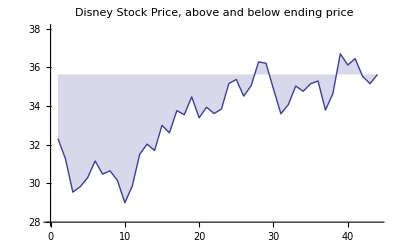

The analysis of each of these regressions really depends on which strike price we are talking about so we will look at them one at a time. All of the plots below were created using actual data, when estimated data is plotted the data came from the OLS estimates of the restricted model (4) that was presented again at the beginning of the section.

### K=33 strike price

The K=33 strike price represents the option that was the most in the money at the time of expiration. The accurate pricing of options that were in the money hypothesis was confirmed by the regression and subsequent tests. Below is a graph showing the actual prices as black dots, the estimated price as a gray line. The blue and red lines represent when the actual price was below and above the estimated price, respectively.

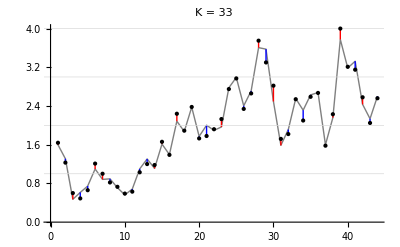

```mathematica
ListPlot[{k33,estR33},Joined->{False,True},PlotLabel->"K = 33",GridLines->{None,{1,2,3,4}},Filling->{1->{{2},{Blue,Red}}},PlotStyle->{Black,Gray},PlotRange->{0,4}]
```

As can be seen in the above plot, the actual price was never very far off the estimated price. In fact the mean deviation from the actual was -2.27×10^-8.  An interesting note that was seen in the testing of the normality of error terms section is that the k=33 option had the strongest evidence of normality. This further supports my first hypothesis. On the other hand, the k=33 call did show signs of heteroskedasticiy in the error terms, which means that the OLS estimation of model parameters was not minimum variance for all linear estimators. This could mean that while the functional form I chose to represent the Black-Scholes equation did well for the in the money call, it is not perfect. In order to see if the same thing would happen with the actual Black-Scholes equation a nonlinear estimation procedure would have to be employed.

### K=34 strike price

The k=34 strike price was also in the money, but not by as much as the k=33 call. The hypothesis of accurate prediction of option prices for in the money calls held in this regression also. Below is a similar plot to the one presented for the k=33 option (in fact, all plots with a label k=xx have the exact same meaning in their lines and colors):

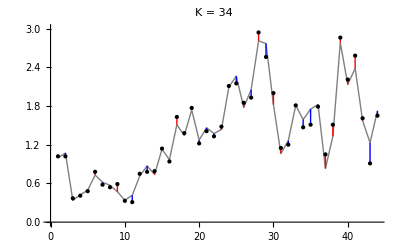

```mathematica
ListPlot[{k34,estR34},Joined->{False,True},PlotLabel->"K = 34",GridLines->{None,{3/4,6/4,9/4,3-.01}},Filling->{1->{{2},{Blue,Red}}},PlotStyle->{Black,Gray},PlotRange->{0,3}]
```

Results for the k=34 are very similar to the k=33. I didn’t get much further insight from this particular regression that I didn’t also get from the k=33 call.

### K=35 strike price

This was the last option examined that was in the money. Again, the hypothesis that my model could accurately predict the price of an in the money call was verified by the results obtained from this regression. Below is a plot similar to those above:

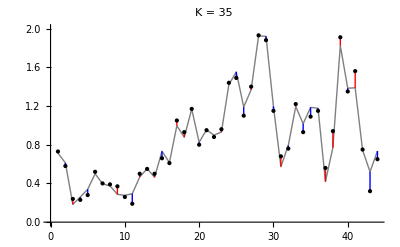

```mathematica
ListPlot[{k35,estR35},Joined->{False,True},GridLines->{None,{1/2,1,3/2,2-.01}},PlotLabel->"K = 35",Filling->{1->{{2},{Blue,Red}}},PlotStyle->{Black,Gray},PlotRange->{0,2}]
```

As in the other two in the money cases we see that the very high R^2 obtained in the regression leads to very good estimates for the actual price.

### K=36 strike price

The k=36 strike price call option was the first of all the options I looked at that was out of the money. The hypothesis that the model would do a poor job at estimating the price for an out of the money option did not hold as you will be able to immediately see from the graph below.

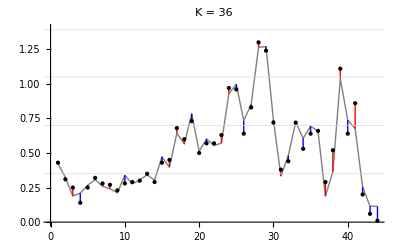

```mathematica
ListPlot[{k36,estR36},Joined->{False,True},PlotLabel->"K = 36",GridLines->{None,{1.4/4,2.8/4,4.2/4,1.4-.01}},Filling->{1->{{2},{Blue,Red}}},PlotStyle->{Black,Gray},PlotRange->{0,1.4}]
```

As would be expected, the value of the call fell to almost zero as the time until expiration fell to zero. This is natural because the option is only worth money if the strike price is below the stock price and for this situation this was not the case. However, the idea that the model wouldn’t predict this was wrong. As the option price moves down to zero so does the estimated price. The thing that made this option different from the rest was that it was the only one where we could reject the hypothesis of normally distributed error terms. This could be corrected easily by modifying the model to include/exclude certain variables, but to maintain consistency with the other options in this project, I chose not to do that here.

### K=37 strike price

The last option we looked at was the November 2011 37 call option. This was the furthest from being in the money and if my hypothesis were true my model should have had the hardest time predicting correct values for this model. As can been seen, this again is not true:

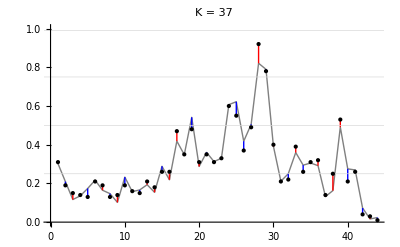

```mathematica
ListPlot[{k37,estR37},Joined->{False,True},PlotLabel->"K = 37",Filling->{1->{{2},{Blue,Red}}},GridLines->{None,{.25,.5,.75,1-.01}},PlotStyle->{Black,Gray},PlotRange->{0,1}]
```

### Overall Analysis and Comments

Perhaps the most surprising thing my data showed was a Negative relationship between the stock price and the price of the call option, regardless of whether or not that option was in or out of the money. I am not sure how to reconcile that finding with theory, but one thing that may have lead to incorrect results in my regression analysis was the small amount of data. According to the central limit theorem of statistical theory as the number of observations increases, the bias and variance for the estimate reach a minimum. If I had the opportunity to do a similar analysis I would gather data for the entire trading life of the option, or at least much more than 44 days.

Another surprise was that the coefficient in front of σ was negative for all but the k=37 strike price. It makes sense that the k=37 would have the biggest positive response to volatility because the buyers of the call will see the increase in volatility as a hope for the option moving into the money. The negative coefficient for each of the other calls is against what I expected before doing the project. One other note about the σ coefficients is that they get bigger and bigger as the strike price rises, which would be expected.

Partially consistent with previous belief the coefficient for the time variable was negative. I thought that the sign would be (-) for in the money options and (+) for out of the money options, but my results showed that it was (-) for all of them. Completely consistent with what I thought the interest rate had a negative effect on the price of the call premium. For reasons explained previously, this makes intuitive theoretical sense.

## V. Summary

This study began with the hypothesis that the Black Scholes model could accurately predict the price of a call option premium that was in the money, but might be less accurate for out of the money options. The results from my analysis showed that my abstraction of the Black Scholes equation was very good at predicting the price of options regardless of their being in or out of the money. It has also been shown that the model chosen was good at estimating the price of a call option up until time of expiration. It is curious that a model created with little or no theoretical foundation (at the time) is very good at predicting the behavior of human decision making in a market for risky assets. The recent financial downturn has shed light on some of the dangers associated with this type  of “quant” analysis and strategy, but working these bugs out of our model will greatly increase the overall efficiency of the world economy.

Surprising results for the signs of various parameters were obtained, and I believe that would most likely reverse itself given a bigger data set. Opportunities for further exploration should start here. A larger data set will decrease the variance of the results and also allow for a more accurate prediction of the actual value for parameter estimates. It would also be interesting to examine put options instead of just calls. Another direction for further study could be to see if the model is good at predicting option prices for stocks with higher volatilities. Disney is a so called “blue-Chip” stock that has had a relatively stable stock price for years. Venturing into a more volatile market like technology or information systems would provide a more rigorous test for the robustness of the Black Scholes model.

## VI. References

Wikipedia article “Call Option”. URL: http://en.wikipedia.org/wiki/Call_option

Wikipedia article “Fischer Black”. URL: http://en.wikipedia.org/wiki/Fischer_Black

Wikipedia article “Black-Scholes”. URL: http://en.wikipedia.org/wiki/Black%E2%80%93Scholes

Mauler, David. “Pricing a Call-Option Premium: A Regression Approach, With an Analysis of Resulting Greeks”, 2008. Brigham Young University.

## VII. Appendix

### Data Sources

Stock Price Data taken from Yahoo Finance. URL: http://finance.yahoo.com/q/hp?s=DIS+Historical+Prices

Options data obtained from Bloomberg.

Treasury Bill data taken from US treasury board. URL: http://www.treasury.gov/resource-center/data-chart-center/interest-rates/Pages/TextView.aspx?data=billrates

### Relevant STATA printouts

#### K=33 regression

Original Regression:

Restricted Regression:

Robust Regression

JB Test

LAD regression

Tests for Heteroskedasticity

Tests for Autocorrelation

#### K=34 regression

Original Regression:

Restricted Regression:

Robust Regression

JB Test

LAD regression

Tests for Heteroskedasticity

Tests for Autocorrelation

#### K=35 regression

Original Regression:

Restricted Regression:

Robust Regression

JB Test

LAD regression

Tests for Heteroskedasticity

Tests for Autocorrelation

#### K=36 regression

Original Regression:

Restricted Regression:

Robust Regression

JB Test

LAD regression

Tests for Heteroskedasticity

Tests for Autocorrelation

#### K=37 regression

Original Regression:

Restricted Regression:

Robust Regression

JB Test

LAD regression

Tests for Heteroskedasticity

Tests for Autocorrelation

## Other and Data/Graphs needed

```mathematica
Needs["PlotLegends`"]
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
actual = {k33,k34,k35,k36,k37,p,σ, t, r,estR33,estR34,estR35,estR36,estR37} = Transpose[Rest[Import["Workbook1.csv"]]];
```

```mathematica
Mean[estR33-k33]
```

-2.27273×10^-8

```mathematica
plot33 = ListPlot[{k33,estR33},Joined->{False,True},PlotLabel->"K = 33",GridLines->{None,{1,2,3,4}},Filling->{1->{{2},{Blue,Red}}},PlotStyle->{Black,Gray},PlotRange->{0,4}]
```

-Graphics-

```mathematica
plot34 = ListPlot[{k34,estR34},Joined->{False,True},PlotLabel->"K = 34",GridLines->{None,{3/4,6/4,9/4,3-.01}},Filling->{1->{{2},{Blue,Red}}},PlotStyle->{Black,Gray},PlotRange->{0,3}]
```

-Graphics-

```mathematica
plot35 = ListPlot[{k35,estR35},Joined->{False,True},GridLines->{None,{1/2,1,3/2,2-.01}},PlotLabel->"K = 35",Filling->{1->{{2},{Blue,Red}}},PlotStyle->{Black,Gray},PlotRange->{0,2}]
```

-Graphics-

```mathematica
plot36 =ListPlot[{k36,estR36},Joined->{False,True},PlotLabel->"K = 36",GridLines->{None,{1.4/4,2.8/4,4.2/4,1.4-.01}},Filling->{1->{{2},{Blue,Red}}},PlotStyle->{Black,Gray},PlotRange->{0,1.4}]
```

-Graphics-

```mathematica
plot37 = ListPlot[{k37,estR37},Joined->{False,True},PlotLabel->"K = 37",Filling->{1->{{2},{Blue,Red}}},GridLines->{None,{.25,.5,.75,1-.01}},PlotStyle->{Black,Gray},PlotRange->{0,1}]
```

-Graphics-

```mathematica
displot = ListPlot[p,Joined->True,PlotRange->{28,38},Filling->{1->35.63},PlotLabel->"Disney Stock Price, above and below ending price"]
```

-Graphics-

```mathematica
Show[{displot,Listplot[k36]}]
```

Show::gcomb: Could not combine the graphics objects in {GraphicsBox[GraphicsComplexBox[List[List[1.`, 32.31`], List[2.`, 31.28`], List[3.`, 29.55`], List[4.`, 29.83`], List[5.`, 30.3`], List[6.`, 31.16`], List[7.`, 30.48`], List[8.`, 30.65`], List[9.`, 30.16`], List[10.`, 29.`], List[11.`, 29.86`], List[12.`, 31.51`], List[13.`, 32.03`], List[14.`, 31.7`], List[15.`, 33.`], List[16.`, 32.61`], List[17.`, 33.76`], List[18.`, 33.55`], List[19.`, 34.47`], List[20.`, 33.39`], List[21.`, 33.94`], List[22.`, 33.61`], List[23.`, 33.84`], List[24.`, 35.16`], List[25.`, 35.37`], List[26.`, 34.51`], List[27.`, 35.05`], List[28.`, 36.28`], List[29.`, 36.21`], List[30.`, 34.88`], List[31.`, 33.6`], List[32.`, 34.07`], List[33.`, 35.03`], List[34.`, 34.76`], List[35.`, 35.15`], List[36.`, 35.29`], List[37.`, 33.79`], List[38.`, 34.64`], List[39.`, 36.7`], List[40.`, 36.12`], List[41.`, 36.45`], List[42.`, 35.53`], List[43.`, 35.15`], List[44.`, 35.63`], List[27.47154471544716`, 35.63`], List[29.43609022556391`, 35.63`], List[38.480582524271846`, 35.63`], List[41.891304347826086`, 35.63`], List[1.`, 35.63`]], List[List[List[EdgeForm[], Directive[Skeleton[1]], GraphicsGroupBox[Skeleton[1]]], List[EdgeForm[], Directive[Skeleton[1]], GraphicsGroupBox[Skeleton[1]]], List[], List[]], List[List[], List[], List[Hue[Skeleton[3]], LineBox[Skeleton[1]]]]]], List[Rule[AspectRatio, NCache[Power[GoldenRatio, -1], 0.6180339887498948`]], Rule[Axes, True], Rule[AxesOrigin, List[0, 28.`]], Rule[PlotLabel, FormBox[.

Show[{-Graphics-,Listplot[{0.43,0.31,0.25,0.14,0.25,0.32,0.28,0.27,0.23,0.28,0.29,0.3,0.35,0.29,0.43,0.45,0.68,0.6,0.73,0.5,0.57,0.57,0.63,0.97,0.96,0.64,0.83,1.3,1.24,0.72,0.38,0.44,0.72,0.53,0.64,0.66,0.29,0.52,1.11,0.64,0.86,0.2,0.06,0.01}]}]

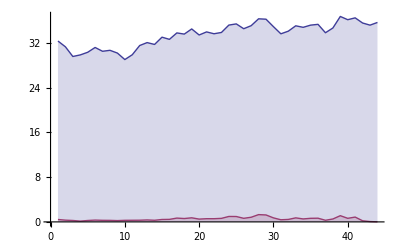

```mathematica
ListPlot[{p,k36},Joined->True,Filling->Axis]
```

```mathematica
Manipulate[Show[plot
```